# MATH223 Final Project

## The Calc-oholics: Calculus in Minecraft

## Part 1: Graphical Generation

## Note: code is generated by Dr. Sell’s COPY-PASTE, ChatGPT, and Trevor Swan. Graphics are to be used in presentation and paper.

### Graphic 1a: Textbook Projectile Motion @ Pi/180 Radians

This Graphic pertains to a firing angle of Pi/180 (1 Deg)

```mathematica
Manipulate[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/180]*t+0,Max[Min[yMax,50],0]},{t,0,Time},PlotRange->{{0,30},{0,2.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 1° Over Time",AspectRatio->1]],{{Time,0.001,"Time (s)"},0.001,0.43352502563127204,0.001,Appearance->"Labeled"}]
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5,t]
```

{{t→-0.332161},{t→0.433525}}

Experimental X-Position: 29.668m @ Pi/180 Radians

```mathematica
Solve[Position ==60.5*Cos[Pi/180]*0.43352502563127204+0, Position]
Solve[Error == (Abs[(29.668-26.2243)]/26.2243)*100,Error]
```

{{Position→26.2243}}

{{Error→13.1317}}

### Graphic 1b: Textbook Projectile Motion @ Pi/36 Radians

This Graphic Pertains to a firing angle of Pi/36 (5 Deg)

```mathematica
Manipulate[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/36]*t+0,Max[Min[yMax,50],0]},{t,0,Time},PlotRange->{{0,47},{0,2.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 5° Over Time",AspectRatio->1]],{{Time,0.001,"Time (s)"},0.001,0.7092368299731663,0.001,Appearance->"Labeled"}]
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5,t]
```

{{t→-0.203035},{t→0.709237}}

Experimental X-Position: 46.603m @ Pi/36 Radians

```mathematica
Solve[Position ==60.5*Cos[Pi/36]*0.7092368299731663+0, Position]
Solve[Error == (Abs[(46.603-42.7433)]/42.7433)*100,Error]
```

{{Position→42.7455}}

{{Error→9.02995}}

### Graphic 1c: Textbook Projectile Motion @ Pi/18 Radians

This Graphic Pertains to a firing angle of Pi/18 (10 Deg)

```mathematica
Manipulate[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/18]*t+0,Max[Min[yMax,50],0]},{t,0,Time},PlotRange->{{0,72},{0,6}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 10° Over Time",AspectRatio->1]],{{Time,0.001,"Time (s)"},0.001,1.1353801946185238,0.01,Appearance->"Labeled"}]
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5,t]
```

{{t→-0.12683},{t→1.13538}}

Experimental X-Position: 64.382m @ Pi/18 Radians

```mathematica
Solve[Position ==60.5*Cos[Pi/18]*1.1353801946185238+0, Position]
Solve[Error == (Abs[(64.382-67.6469)]/67.6469)*100,Error]
```

{{Position→67.6469}}

{{Error→4.82639}}

### Graphic 1d: Textbook Projectile Motion @ 1.4Pi/18 Radians

This Graphic Pertains to a firing Angle of 1.4Pi/18 Radians (14 Deg)

```mathematica
Manipulate[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5,50];
ParametricPlot[{60.5*Cos[(1.4*Pi)/18]*t+0,Max[Min[yMax,50],0]},{t,0,Time},PlotRange->{{0,90},{0,7.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 14° Over Time",AspectRatio->1]],{{Time,0.001,"Time (s)"},0.001,1.5010195635305104,0.01,Appearance->"Labeled"}]
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5,t]
```

{{t→-0.0959349},{t→1.50102}}

Experimental X-Position: 74.489m @ 1.4Pi/18 Radians

```mathematica
Solve[Position ==60.5*Cos[(1.4*Pi)/18]*1.5010195635305104+0, Position]
Solve[Error == (Abs[(74.489-88.1142)]/88.1142)*100,Error]
```

{{Position→88.1142}}

{{Error→15.4631}}

### Graphic 2: Basic Vector Field Plot that acts on Arrows

Note: For this Graphic, Arrows are assumed to slow by a factor of 0.8666666666666665m/s every game tick (calculated in Misc), being affected by a gravity of 20.8333m/s
	At any point in Time, the Arrow’s being affected by the force F(x,y) = <-0.99x,-20.83y>

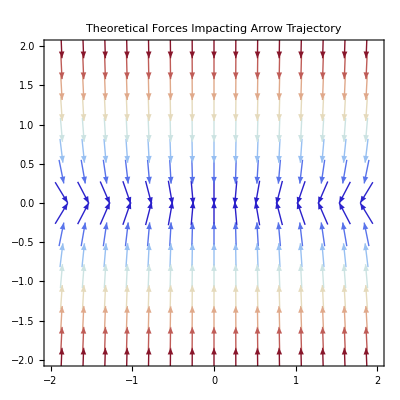

```mathematica
(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

VectorPlot[F[x,y],{x,-2,2},{y,-2,2},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotLabel->"Theoretical Forces Impacting Arrow Trajectory"]
```

### Graphic 3a: Textbook Projectile Curve Over vector Field (Pi/180 Radians) - Referencing 1a

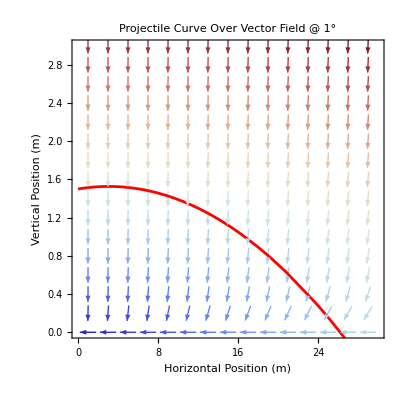

```mathematica
(*Define the parametric curve*)
parametricCurve[t_]:={60.5*Cos[Pi/180]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5}

(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

(*Create a vector field plot*)
vectorFieldPlot=VectorPlot[F[x,y],{x,0,30},{y,0,3},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotRange->All,PlotLabel->"Projectile Curve Over Vector Field @ 1°",FrameLabel->{"Horizontal Position (m)","Vertical Position (m)"}];

(*Create a parametric plot for the curve*)
parametricCurvePlot=ParametricPlot[parametricCurve[t],{t,0,20},PlotStyle->Red,PlotLabel->"Parametric Curve"];

(*Show both plots on the same graph*)
Show[vectorFieldPlot,parametricCurvePlot]
```

For Graphic 3a: The Curve C = (0, 1.5) -> (26.2243, 0) on t = [0.001, 0.433525]

### Graphic 3b: Textbook Projectile Curve Over vector Field (Pi/36 Radians) - Referencing 1b

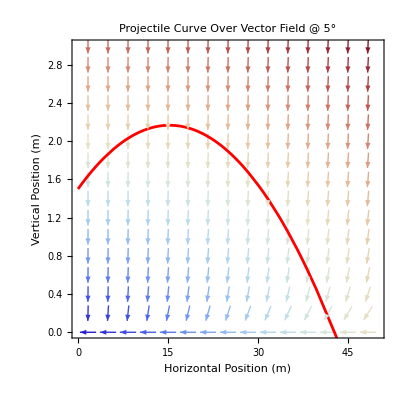

```mathematica
(*Define the parametric curve*)
parametricCurve[t_]:={60.5*Cos[Pi/36]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5}

(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

(*Create a vector field plot*)
vectorFieldPlot=VectorPlot[F[x,y],{x,0,50},{y,0,3},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotRange->All,PlotLabel->"Projectile Curve Over Vector Field @ 5°",FrameLabel->{"Horizontal Position (m)","Vertical Position (m)"}];

(*Create a parametric plot for the curve*)
parametricCurvePlot=ParametricPlot[parametricCurve[t],{t,0,20},PlotStyle->Red,PlotLabel->"Parametric Curve"];

(*Show both plots on the same graph*)
Show[vectorFieldPlot,parametricCurvePlot]
```

For Graphic 3b: The Curve C = (0, 1.5) -> (42.7433, 0) on t = [0.001, 0.7092]

### Graphic 3c: Textbook Projectile Curve Over vector Field (Pi/18 Radians) - Referencing 1c

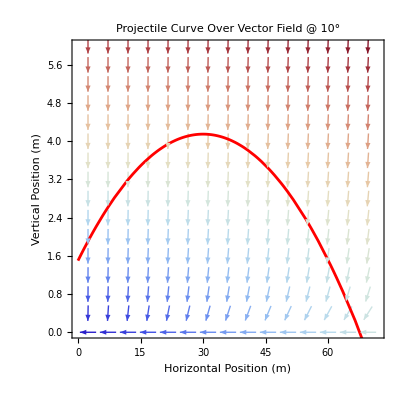

```mathematica
(*Define the parametric curve*)
parametricCurve[t_]:={60.5*Cos[Pi/18]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5}

(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

(*Create a vector field plot*)
vectorFieldPlot=VectorPlot[F[x,y],{x,0,72},{y,0,6},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotRange->All,PlotLabel->"Projectile Curve Over Vector Field @ 10°",FrameLabel->{"Horizontal Position (m)","Vertical Position (m)"}];

(*Create a parametric plot for the curve*)
parametricCurvePlot=ParametricPlot[parametricCurve[t],{t,0,20},PlotStyle->Red,PlotLabel->"Parametric Curve"];

(*Show both plots on the same graph*)
Show[vectorFieldPlot,parametricCurvePlot]
```

For Graphic 3c: The Curve C = (0, 1.5) -> (67.6469, 0) on t = [0.001, 1.13538]

### Graphic 3d: Textbook Projectile Curve Over vector Field (1.4Pi/18 Radians) - Referencing 1d

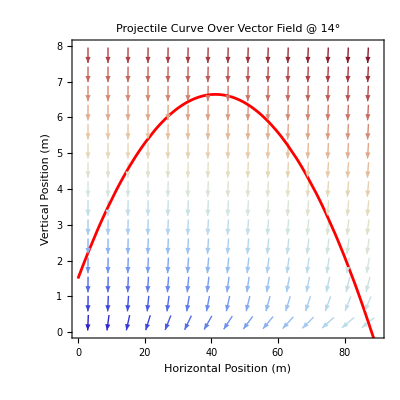

```mathematica
(*Define the parametric curve*)
parametricCurve[t_]:={60.5*Cos[(1.4*Pi)/18]*t,-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5}

(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

(*Create a vector field plot*)
vectorFieldPlot=VectorPlot[F[x,y],{x,0,90},{y,0,8},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotRange->All,PlotLabel->"Projectile Curve Over Vector Field @ 14°",FrameLabel->{"Horizontal Position (m)","Vertical Position (m)"}];

(*Create a parametric plot for the curve*)
parametricCurvePlot=ParametricPlot[parametricCurve[t],{t,0,20},PlotStyle->Red,PlotLabel->"Parametric Curve"];

(*Show both plots on the same graph*)
Show[vectorFieldPlot,parametricCurvePlot]
```

For Graphic 3d: The Curve C = (0, 1.5) -> (88.1142, 0) on t = [0.001, 1.50102]

### Graphic 4: Displaying Horizontal Decay of An Arrow

This code is Not Necessarily Useful, and Was generated entirely by ChatGPT

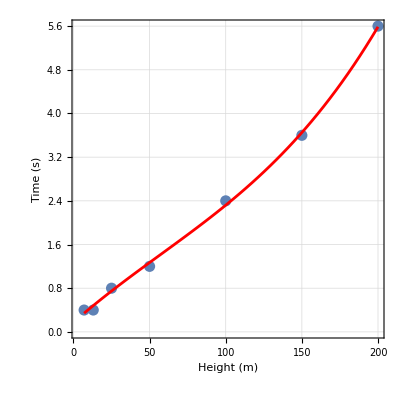
-Graphics-Time Taken for An Arrow to Travel Set Distances

```mathematica
(*Experimental data points*)
data={{7,0.4},{13,0.4},{25,0.8},{50,1.2},{100,2.4},{150,3.6},{200,5.6}};
(*Scatter plot*)
scatterPlot=ListPlot[data,PlotStyle->PointSize[0.02],PlotRange->All,Frame->True,Axes->False,AspectRatio->1];
(*Fit a line to the data*)
fitPoly=Fit[data,{1,x,x^2,x^3},x];
(*Plot the line of best fit*)
lineOfBestFit=Plot[fitPoly,{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Red];
(*Combine the scatter plot and the line of best fit*)
plot=Show[scatterPlot,lineOfBestFit,FrameLabel->{"Height (m)","Time (s)"},GridLines->Automatic];
(*Add a title*)
title="Time Taken for An Arrow to Travel Set Distances";
finalPlot=Labeled[plot,title,{{Top,Center}}];
(*Display the plot*)
finalPlot
```

## Part 2: Graphic Animation Exports

## Note: This Section Allows the Variations of Graphic 1 to be Exported. It is ChatGPT Assisted.

### Graphic 1a Export - 1Deg

```mathematica
animation1=Table[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/180]*t+0,Max[Min[yMax,50],0]},{t,0,time},PlotRange->{{0,30},{0,2.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 1° Over Time",AspectRatio->1]],{time,0.001,0.43352502563127204,0.01}];

Export["1Deg_Curve.gif",animation1];
```

### Graphic 1b Export - 5Deg

```mathematica
animation2=Table[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/36]*t+0,Max[Min[yMax,50],0]},{t,0,time},PlotRange->{{0,47},{0,2.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 5° Over Time",AspectRatio->1]],{time,0.001,0.7092368299731663,0.01}];

Export["5Deg_Curve.gif",animation2];
```

### Graphic 1c Export - 10Deg

```mathematica
animation3=Table[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5,50];
ParametricPlot[{60.5*Cos[Pi/18]*t+0,Max[Min[yMax,50],0]},{t,0,time},PlotRange->{{0,72},{0,6}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 10° Over Time",AspectRatio->1]],{time,0.001,1.1353801946185238,0.01}];

Export["10Deg_Curve.gif",animation3];
```

### Graphic 1d Export - 14Deg

```mathematica
animation4=Table[Module[{yMax},yMax=Min[-0.5 (20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5,50];
ParametricPlot[{60.5*Cos[(1.4*Pi)/18]*t+0,Max[Min[yMax,50],0]},{t,0,time},PlotRange->{{0,90},{0,7.5}},AxesLabel->{"X Position","Y Position"},PlotLabel->"Position of an Arrow Fired at 14° Over Time",AspectRatio->1]],{time,0.001,1.5010195635305104,0.01}];

Export["14Deg_Curve.gif",animation4];
```

## Part 3: Gravitational Calculations

## Note: code is generated using a MATLAB script that takes data as an input

### Finding Gravity of a Player

```mathematica
Off[Solve::ifun]
Solve[20000==78.369906*257.6+(78.369906^2)*(1/g)*(Exp[-g*257.6/78.369906]-1),g]

Solve[dt==(-78.369906*(1-Exp[-32.6541000*(257.6/78.369906)]))/(((78.369906^2)/(32.6541000^2))*(1-Exp[-32.6541000*(257.6/78.369906)])-((257.6*78.369906)/32.6541000)*(Exp[-32.6541000*(257.6/78.369906)])),dt]

Solve[dv==(257.6+2*(78.369906/32.6541000)*Exp[-32.6541000*(257.6/78.369906)]+257.6*Exp[-32.6541000*(257.6/78.369906)]-2*(78.369906)/(32.6541000))/(((78.369906^2)/(32.6541000^2))*(1-Exp[-32.6541000*(257.6/78.369906)])-((257.6*78.369906)/32.6541000)*(Exp[-32.6541000*(257.6/78.369906)])),dv]

Solve[uncert ==Sqrt[13.6059000*0.4^2+43.8888000*0.2456737^2],uncert]
```

{{g→32.6541}}

{{dt→-13.6059}}

{{dv→43.8888}}

{{uncert→12.078}}

### Finding Gravity of an Arrow

```mathematica
Off[Solve::ifun]
Solve[20000==100.000000*204.8+(100.000000^2)*(1/g)*(Exp[-g*204.8/100.000000]-1),g]

Solve[dt==(-100.000000*(1-Exp[-20.8333000*(204.8/100.000000)]))/(((100.000000^2)/(20.8333000^2))*(1-Exp[-20.8333000*(204.8/100.000000)])-((204.8*100.000000)/20.8333000)*(Exp[-20.8333000*(204.8/100.000000)])),dt]

Solve[dv==(204.8+2*(100.000000/20.8333000)*Exp[-20.8333000*(204.8/100.000000)]+204.8*Exp[-20.8333000*(204.8/100.000000)]-2*(100.000000)/(20.8333000))/(((100.000000^2)/(20.8333000^2))*(1-Exp[-20.8333000*(204.8/100.000000)])-((204.8*100.000000)/20.8333000)*(Exp[-20.8333000*(204.8/100.000000)])),dv]

Solve[uncert==Sqrt[-4.3402600*0.4^2+8.4721900*0.4000000^2],uncert]
```

{{g→20.8333}}

{{dt→-4.34026}}

{{dv→8.47219}}

{{uncert→0.813086}}

### Finding Gravity of Item

```mathematica
Solve[20000==40.000000*502.0+(40.000000^2)*(1/g)*(Exp[-g*502.0/40.000000]-1),g]

Solve[dt==(-40.000000*(1-Exp[-20.0000000*(502.0/40.000000)]))/(((40.000000^2)/(20.0000000^2))*(1-Exp[-20.0000000*(502.0/40.000000)])-((502.0*40.000000)/20.0000000)*(Exp[-20.0000000*(502.0/40.000000)])),dt]

Solve[dv==(502.0+2*(40.000000/20.0000000)*Exp[-20.0000000*(502.0/40.000000)]+502.0*Exp[-20.0000000*(502.0/40.000000)]-2*(40.000000)/(20.0000000))/(((40.000000^2)/(20.0000000^2))*(1-Exp[-20.0000000*(502.0/40.000000)])-((502.0*40.000000)/20.0000000)*(Exp[-20.0000000*(502.0/40.000000)])),dv]

Solve[uncert==Sqrt[10.0000000*0.4^2+124.5000000*0.0642053^2],uncert]
```

{{g→20.}}

{{dt→-10.}}

{{dv→124.5}}

{{uncert→1.45369}}

### Finding Gravity of Armor Stand

```mathematica
Off[Solve::ifun]
Solve[20000==78.369906*257.6+(78.369906^2)*(1/g)*(Exp[-g*257.6/78.369906]-1),g]

Solve[dt==(-78.369906*(1-Exp[-32.6541000*(257.6/78.369906)]))/(((78.369906^2)/(32.6541000^2))*(1-Exp[-32.6541000*(257.6/78.369906)])-((257.6*78.369906)/32.6541000)*(Exp[-32.6541000*(257.6/78.369906)])),dt]

Solve[dv==(257.6+2*(78.369906/32.6541000)*Exp[-32.6541000*(257.6/78.369906)]+257.6*Exp[-32.6541000*(257.6/78.369906)]-2*(78.369906)/(32.6541000))/(((78.369906^2)/(32.6541000^2))*(1-Exp[-32.6541000*(257.6/78.369906)])-((257.6*78.369906)/32.6541000)*(Exp[-32.6541000*(257.6/78.369906)])),dv]

Solve[uncert==Sqrt[13.6059000*0.4^2+43.8888000*0.2456737^2],uncert]
```

{{g→32.6541}}

{{dt→-13.6059}}

{{dv→43.8888}}

{{uncert→2.19679}}

### Finding Gravity of Sand

```mathematica
Off[Solve::ifun]
Solve[5000==40.002560*127.2+(40.002560^2)*(1/g)*(Exp[-g*127.2/40.002560]-1),g]

Solve[dt==(-40.002560*(1-Exp[-18.1171000*(127.2/40.002560)]))/(((40.002560^2)/(18.1171000^2))*(1-Exp[-18.1171000*(127.2/40.002560)])-((127.2*40.002560)/18.1171000)*(Exp[-18.1171000*(127.2/40.002560)])),dt]

Solve[dv==(127.2+2*(40.002560/18.1171000)*Exp[-18.1171000*(127.2/40.002560)]+127.2*Exp[-18.1171000*(127.2/40.002560)]-2*(40.002560)/(18.1171000))/(((40.002560^2)/(18.1171000^2))*(1-Exp[-18.1171000*(127.2/40.002560)])-((127.2*40.002560)/18.1171000)*(Exp[-18.1171000*(127.2/40.002560)])),dv]

Solve[uncert==Sqrt[8.2052100*0.4^2+25.1851000*0.3200000^2],uncert]
```

{{g→18.1171}}

{{dt→-8.20521}}

{{dv→25.1851}}

{{uncert→1.97276}}

## Part 4: Miscellaneous Calculations and Graphics

## Note: This Section contains ‘random’, but necessary, calculations from throughout the project

### Proving Junity’s Result for the constant ‘mu’

x(t)=v_x*u*(1-e^(-t/u))https://youtu.be/CQ-tqYPiMfQ?si=ixBtusouctiP1aDY&t=704Nonehttps://youtu.be/CQ-tqYPiMfQ?si=ixBtusouctiP1aDY&t=704HyperlinkActionRecycledHyperlinkActive and  y(t)=(v_y+v)u(1-e^(-t/u))-vt+y_0

```mathematica
Off[FindRoot::lstol]
(*mu value for an arrow in the x direction*)
Clear[mu1];
FindRoot[200==60.5*mu1*(1-Exp[-5.6/mu1]),{mu1,1}]

(*mu vlaue for an arrow in the y direction*)
Clear[mu2];
FindRoot[0 == (0
+100)*mu2*(1-Exp[-204.8/mu2])-100*204.8+20000,{mu2,3.8}]
```

{mu1→4.8016}

{mu2→4.8}

### Testing Different Objects ‘mu’ Values

#### Player’s Mu Value

```mathematica
Off[FindRoot::lstol]
(*mu value for a Player in the y direction*)
Clear[mu2];
FindRoot[0 == (0+
78.369906)*mu2*(1-Exp[-257.6/mu2])-78.369906*257.6+20000,{mu2,4.8}]
```

{mu2→2.4}

#### Sand’s Mu Value

```mathematica
Off[FindRoot::lstol]
(*mu value for a Falling Blocks in the y direction*)
Clear[mu2];
FindRoot[0 == (0+
40)*mu2*(1-Exp[-127.2/mu2])-40*127.2+5000,{mu2,4.8}]
```

{mu2→2.2}

#### Item’s Mu Value

```mathematica
Off[FindRoot::lstol]
(*mu value for an Item in the y direction*)
Clear[mu2];
FindRoot[0 == (0+
40)*mu2*(1-Exp[-502/mu2])-40*502+20000,{mu2,4.8}]
```

{mu2→2.}

### Graphic 4a: Arrows Trajectory as an Exponential

#### Manipulable Parametric Curve

```mathematica
Off[Solve::ifun]
Manipulate[ParametricPlot[{60.5*4.8*(1-Exp[-t/4.8]),((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)},{t,0,tMax},PlotRange->{{0,30},{0,2}},AxesLabel->{"X Position","Y Position"},AspectRatio->1,PlotLabel->"Trajectory of an Arrow at a Horizontal Firing Angle",GridLines->Automatic,GridLinesStyle->LightGray],{{tMax,0.001,"Time (s)"},0.001,0.3845398978092346,Appearance->"Labeled"} ]
Solve[0==(0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5,t]
```

{{t→-0.374539},{t→0.38454}}

Experimental X-Position: 25.370m @ 0 Radians

```mathematica
Solve[Position ==60.5*4.8*(1-Exp[-0.3845398978092346/4.8]), Position]
Solve[Error == (Abs[(25.370-22.35716381745867)]/22.35716381745867)*100,Error]
```

{{Position→22.3572}}

{{Error→13.4759}}

Compared to the error of the trigonometric projectile motion (13.1317%) this equation is not bad. Its main downfall is the lack of ability to adjust the firing angle of the arrow.

#### Exporting Exponential Trajectory GIF

```mathematica
animation5=Table[ParametricPlot[{60.5*4.8*(1-Exp[-t/4.8]),((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)},{t,0,time},PlotRange->{{0,30},{0,2}},AxesLabel->{"X Position","Y Position"},AspectRatio->1,PlotLabel->"Trajectory of an Arrow at a Horizontal Firing Angle",GridLines->Automatic,GridLinesStyle->LightGray],{time,0.001,0.3845398978092346,0.01}];

Export["Exp_Trajectory_Curve.gif",animation5];
```

### Graphic 4b: Exponential Trajectory over a Vector Field

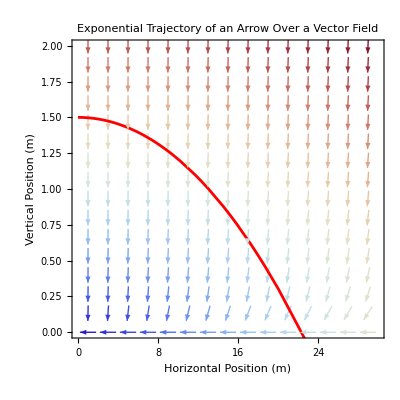

```mathematica
(*Define the parametric curve*)
parametricCurve[t_]:={(60.5*4.8*(1-Exp[-t/4.8])),((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)}

(*Define the vector field function*)
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}

(*Create a vector field plot*)
vectorFieldPlot=VectorPlot[F[x,y],{x,0,30},{y,0,2},VectorScale->Small,VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotRange->All,PlotLabel->"Exponential Trajectory of an Arrow Over a Vector Field",FrameLabel->{"Horizontal Position (m)","Vertical Position (m)"}];

(*Create a parametric plot for the curve*)
parametricCurvePlot=ParametricPlot[parametricCurve[t],{t,0,20},PlotStyle->Red,PlotLabel->"Parametric Curve"];

(*Show both plots on the same graph*)
Show[vectorFieldPlot,parametricCurvePlot]
```

### Mass Calculations

```mathematica
(*Steve*)
Solve[Steve==291.7*(-32.65412555555556/-9.81),Steve]

(*Arrow*)
Solve[Arrow == 30*(-20.833333333333332/-9.81),Arrow]

(*Diamond Sword*)
Solve[Sword == (3514.00/9)*2+(232.5*2)/4,Sword]
```

{{Steve→970.969}}

{{Arrow→63.7105}}

{{Sword→897.139}}

### Attempting to find Rate of Change for Arrow Horizontal

```mathematica
Solve[RoC ==((5.6-3.6)+ (3.6-2.4)+(2.4-1.2)+(1.2-0.8)+(0.8-0.4)+0)/6,RoC]
```

{{RoC→0.866667}}

### Flow and Flux Calculations over F(x,y) = <-0.87x, -20.83y> Using Various Curves

#### For Graphic 3a: The Curve C = (0, 1.5) -> (26.2243, 0) on t = [0.001, 0.433525]

```mathematica
(*r(t) = <26.2243t,-1.5t+1.5> on 0 < t < 1*)
```

```mathematica
Flow->Integrate[Dot[{-0.87*26.2243*t,-20.83*(-1.5*t+1.5)},{26.2243,-1.5}],{t,0,1}] ;
Flux->Integrate[Dot[{-0.87*26.2243*t,-20.83*(-1.5*t+1.5)},{-1.5,-26.2243}],{t,0,1}]; (*Flux is not Path Independent!*)
```

```mathematica
(*r(t) = <60.5*Cos[Pi/180]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5>*)
```

```mathematica
Flow -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/180]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5)},{D[60.5*Cos[Pi/180]*t,{t,1}],D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5,{t,1}]}],{t,0.001,0.433525}]
Flux -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/180]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5)},{D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/180]*t+1.5,{t,1}],-1*D[60.5*Cos[Pi/180]*t,{t,1}]}],{t,0.001,0.433525}]
```

Flow→-275.687

Flux→610.591

#### For Graphic 3b: The Curve C = (0, 1.5) -> (42.7433, 0) on t = [0.001, 0.7092]

```mathematica
(*r(t) = <42.7433t,-1.5t+1.5> on 0 < t < 1*)
```

```mathematica
Flow->Integrate[Dot[{-0.87*42.7433*t,-20.83*(-1.5*t+1.5)},{42.7433,-1.5}],{t,0,1}] ;
Flux->Integrate[Dot[{-0.87*42.7433*t,-20.83*(-1.5*t+1.5)},{-1.5,-42.7433}],{t,0,1}];(*Flux is not Path Independent!*)
```

```mathematica
(*r(t) = <60.5*Cos[Pi/36]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5>*)
Flow -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/36]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5)},{D[60.5*Cos[Pi/36]*t,{t,1}],D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5,{t,1}]}],{t,0.001,0.7092}]
Flux -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/36]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5)},{D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/36]*t+1.5,{t,1}],-1*D[60.5*Cos[Pi/36]*t,{t,1}]}],{t,0.001,0.7092}]
```

Flow→-771.141

Flux→1503.83

#### For Graphic 3c: The Curve C = (0, 1.5) -> (67.6469, 0) on t = [0.001, 1.13538]

```mathematica
(*r(t) = <67.6469t,-1.5t+1.5> on 0 < t < 1*)
```

```mathematica
Flow->Integrate[Dot[{-0.87*67.6469*t,-20.83*(-1.5*t+1.5)},{67.6469,-1.5}],{t,0,1}]; 
Flux->Integrate[Dot[{-0.87*67.6469*t,-20.83*(-1.5*t+1.5)},{-1.5,-67.6469}],{t,0,1}]; (*Flux is not Path Independent!*)
```

```mathematica
(*r(t) = <60.5*Cos[Pi/18]*t,-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5>*)
Flow -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/18]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5)},{D[60.5*Cos[Pi/18]*t,{t,1}],D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5,{t,1}]}],{t,0.001,1.13538}]
Flux -> Integrate[Dot[{-0.87*(60.5*Cos[Pi/18]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5)},{D[-0.5*(20.8333*t^2)+60.5*Sin[Pi/18]*t+1.5,{t,1}],-1*D[60.5*Cos[Pi/18]*t,{t,1}]}],{t,0.001,1.13538}]
```

Flow→-1966.84

Flux→4384.33

#### For Graphic 3d: The Curve C = (0, 1.5) -> (88.1142, 0) on t = [0.001, 1.50102]

```mathematica
(*r(t) = <88.1142t,-1.5t+1.5> on 0 < t < 1*)
```

```mathematica
Flow->Integrate[Dot[{-0.87*88.1142*t,-20.83*(-1.5*t+1.5)},{88.1142,-1.5}],{t,0,1}] ;
Flux->Integrate[Dot[{-0.87*88.1142*t,-20.83*(-1.5*t+1.5)},{-1.5,-88.1142}],{t,0,1}]; (*Flux is not Path Independent!*)
```

```mathematica
(*r(t) = <60.5*Cos[(1.4*Pi)/180]*t,-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5>*)
```

```mathematica
Flow -> Integrate[Dot[{-0.87*(60.5*Cos[(1.4*Pi)/18]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5)},{D[60.5*Cos[(1.4*Pi)/18]*t,{t,1}],D[-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5,{t,1}]}],{t,0.001,1.50102}]
Flux -> Integrate[Dot[{-0.87*(60.5*Cos[(1.4*Pi)/18]*t),-20.83*(-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5)},{D[-0.5*(20.8333*t^2)+60.5*Sin[(1.4*Pi)/18]*t+1.5,{t,1}],-1*D[60.5*Cos[(1.4*Pi)/18]*t,{t,1}]}],{t,0.001,1.50102}]
```

Flow→-3353.5

Flux→8911.42

#### For Graphic 4b: The Curve C = (0, 1.5) -> (22.35716381745867, 0) on t = [0.001, 0.3845398978092346]

```mathematica
(*r(t) = <60.5*4.8*(1-Exp[-t/4.8]),((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)>*)
```

```mathematica
Flow -> Integrate[Dot[{-0.87*(60.5*4.8*(1-Exp[-t/4.8])),-20.83*((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)},{D[60.5*4.8*(1-Exp[-t/4.8]),{t,1}],D[((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5),{t,1}]}],{t,0.001,0.3845398978092346}]
Flux -> Integrate[Dot[{-0.87*(60.5*4.8*(1-Exp[-t/4.8])),-20.83*((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5)},{D[((0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5),{t,1}],-1*D[(60.5*4.8*(1-Exp[-t/4.8])),{t,1}]}],{t,0.001,0.3845398978092346}]
```

Flow→-193.997

Flux→486.507

### Graphic 5: Manipulable Vector Field Plot

```mathematica
F[x_,y_,t_]:={-0.8666666666666665 x,-20.83 y}
scale[t_]:=0.01+0.04 t

Manipulate[VectorPlot[F[x,y,t],{x,-2,2},{y,-2,2},VectorScale->scale[t],VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotLabel->"Theoretical Forces Impacting Arrow Trajectory"],{t,0,1,0.001}]
```

#### Animating the Arrows of the Vector Field Plot

```mathematica
F[x_,y_]:={-0.8666666666666665 x,-20.83 y}
scale[t_]:=0.01+0.04 t
animation6=Table[VectorPlot[F[x,y],{x,-2,2},{y,-2,2},VectorScale->scale[t],VectorStyle->Arrowheads[0.02],VectorColorFunction->"ThermometerColors",PlotLabel->"Theoretical Forces Impacting Arrow Trajectory"],{t,0,1,0.05}];

Export["Vector_Field_Animated.gif",animation6];
```

### Graphic 6: Percent Error Data

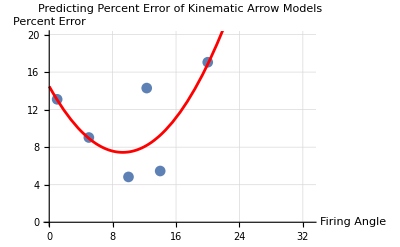

```mathematica
(*Input data*)
data={{1,13.1},{5,9.03},{10,4.83},{14,5.46},{12.3,14.296},{20,17.0499}};

(*Quadratic fit*)
fit=Fit[data,{1,x,x^2},x];

(*Scatter plot with quadratic line of best fit*)
Show[ListPlot[data,PlotLabel->"Predicting Percent Error of Kinematic Arrow Models",AxesLabel->{"Firing Angle","Percent Error"},PlotStyle->PointSize[0.02],PlotMarkers->Automatic,GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->{{0,33},{0,20}}],Plot[fit,{x,0,45},PlotStyle->Red,Epilog->{Text[Style["Quadratic Fit",Red],{20,11}]}]]
```

#### Percent Error Model Testing: 12.3Deg

```mathematica
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[(1.23*Pi)/18]*t+1.5,t]
```

{{t→-0.107112},{t→1.34439}}

Experimental X-Position: 68.108m @ 1.23Pi/18 Radians

```mathematica
Solve[Position ==60.5*Cos[(1.23*Pi)/18]*1.3443940846782658+0, Position]
Solve[Error == (Abs[(68.108-79.46882458927672)]/79.46882458927672)*100,Error]
```

{{Position→79.4688}}

{{Error→14.296}}

#### Percent Error Model Testing: 20Deg

```mathematica
Solve[0 == -0.5 (20.8333*t^2)+60.5*Sin[Pi/9]*t+1.5,t]
```

{{t→-0.0700227},{t→2.05648}}

Experimental X-Position: 96.98m @ Pi/9 Radians

```mathematica
Solve[Position ==60.5*Cos[Pi/9]*2.0564788836392847+0, Position]
Solve[Error == (Abs[(96.98-116.91371092135165)]/116.91371092135165)*100,Error]
```

{{Position→116.914}}

{{Error→17.0499}}

Error Conclusion: There is no correlation and a line of best fit is not appropriate to use here

### Graphic 7: Parametric Curve in Space

```mathematica
ParametricPlot3D[{60.5*4.8*(1-Exp[-t/4.8]),0,(0+100)*4.8*(1-Exp[-t/4.8])-100*t+1.5},{t,0,0.3845398978092346},AxesLabel->{"X","Y","Z"},PlotLabel->"3D Curve: {(60.5*4.8*(1 - Exp[-t/4.8])), ((0 + 100)*4.8*(1 - Exp[-t/4.8]) - 100*t + 1.5)}"];
```

I don’t like the plot above that’s why its suppressed hehe

### Attempting to Find the Units on Flow and Flux